```mathematica
MasterStiffnessOfSixElementBar[kbar_]:=Module[
{K=Table[0,{7},{7}]},K[[1,1]]=K[[7,7]]=kbar;
For [i=2,i≤6,i++,K[[i,i]]=2*kbar];
For [i=1,i≤6,i++,K[[i,i+1]]=K[[i+1,i]]=-kbar];
Return[K]];
```

```mathematica
FixLeftEndOfSixElementBar[Khat_,fhat_]:=Module[
{Kmod=Khat,fmod=fhat},fmod[[1]]=0;Kmod[[1,1]]=1;Kmod[[1,2]]=Kmod[[2,1]]=0;Return[{Kmod,fmod}]];
```

```mathematica
K=MasterStiffnessOfSixElementBar[100];
Print["Stiffness K=",K//MatrixForm];
f={1,2,3,4,5,6,7};Print["Applied forces=",f];
T={{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,1,0,0,0,0},{0,0,0,0,0,1}};
Print["Tranformation matrix T=",T//MatrixForm];
g={0,0,0,0,0,-1/5,0};
Print["Contraint gap vector g=",g];
Khat=Simplify[Transpose[T].K.T];fhat=Simplify[Transpose[T].(f-K.g)];{Kmod,fmod}=FixLeftEndOfSixElementBar[Khat,fhat];Print["Modified Stiffness upon fixing node 1:",Kmod//MatrixForm];
Print["Modified RHS upon fixing node 1:",fmod];umod=LinearSolve[Kmod,fmod];Print["Computed umod (lacks slace u6)=",umod];u=T.umod+g;Print["Complete solution u=",u];Print["Numerical u=",N[u]];fu=K.u;Print["Recovered forces K.u with reactions=",fu];Print["Numerical K.u=",N[fu]];
```

Stiffness K=(100 | -100 | 0 | 0 | 0 | 0 | 0
-100 | 200 | -100 | 0 | 0 | 0 | 0
0 | -100 | 200 | -100 | 0 | 0 | 0
0 | 0 | -100 | 200 | -100 | 0 | 0
0 | 0 | 0 | -100 | 200 | -100 | 0
0 | 0 | 0 | 0 | -100 | 200 | -100
0 | 0 | 0 | 0 | 0 | -100 | 100)

Applied forces={1,2,3,4,5,6,7}

Tranformation matrix T=(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1)

Contraint gap vector g={0,0,0,0,0,-1/5,0}

Modified Stiffness upon fixing node 1:(1 | 0 | 0 | 0 | 0 | 0
0 | 400 | -100 | 0 | -100 | -100
0 | -100 | 200 | -100 | 0 | 0
0 | 0 | -100 | 200 | -100 | 0
0 | -100 | 0 | -100 | 200 | 0
0 | -100 | 0 | 0 | 0 | 100)

Modified RHS upon fixing node 1:{0,48,3,4,-15,-13}

Computed umod (lacks slace u6)={0,27/100,11/40,1/4,37/200,7/50}

Complete solution u={0,27/100,11/40,1/4,37/200,7/100,7/50}

Numerical u={0.,0.27,0.275,0.25,0.185,0.07,0.14}

Recovered forces K.u with reactions={-27,53/2,3,4,5,-37/2,7}

Numerical K.u={-27.,26.5,3.,4.,5.,-18.5,7.}

Master Stiffness K=(100 | -100 | 0 | 0 | 0 | 0 | 0
-100 | 200 | -100 | 0 | 0 | 0 | 0
0 | -100 | 200 | -100 | 0 | 0 | 0
0 | 0 | -100 | 200 | -100 | 0 | 0
0 | 0 | 0 | -100 | 200 | -100 | 0
0 | 0 | 0 | 0 | -100 | 200 | -100
0 | 0 | 0 | 0 | 0 | -100 | 100)

Applied forces={1,2,3,4,5,6,7}

Weight w=1.×10^3

L2 solution error=4.05286×10^-2

Weight w=1.×10^4

L2 solution error=4.14382×10^-3

Weight w=1.×10^5

L2 solution error=4.15314×10^-4

Weight w=1.×10^6

L2 solution error=4.15407×10^-5

Weight w=1.×10^7

L2 solution error=4.15417×10^-6

Weight w=1.×10^8

L2 solution error=4.15403×10^-7

Weight w=1.×10^9

L2 solution error=4.13318×10^-8

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.},{0.,1.×10^10,-100.,0.,0.,-1.×10^10,0.},{0.,-100.,200.,-100.,0.,0.,0.},{0.,0.,-100.,200.,-100.,0.,0.},{0.,0.,0.,-100.,200.,-100.,0.},{0.,-1.×10^10,0.,0.,-100.,1.×10^10,-100.},{0.,0.,0.,0.,0.,-100.,100.}} may contain significant numerical errors.

Weight w=1.×10^10

L2 solution error=7.45618×10^-9

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.},{0.,1.×10^11,-100.,0.,0.,-1.×10^11,0.},{0.,-100.,200.,-100.,0.,0.,0.},{0.,0.,-100.,200.,-100.,0.,0.},{0.,0.,0.,-100.,200.,-100.,0.},{0.,-1.×10^11,0.,0.,-100.,1.×10^11,-100.},{0.,0.,0.,0.,0.,-100.,100.}} may contain significant numerical errors.

Weight w=1.×10^11

L2 solution error=3.51145×10^-8

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.},{0.,1.×10^12,-100.,0.,0.,-1.×10^12,0.},{0.,-100.,200.,-100.,0.,0.,0.},{0.,0.,-100.,200.,-100.,0.,0.},{0.,0.,0.,-100.,200.,-100.,0.},{0.,-1.×10^12,0.,0.,-100.,1.×10^12,-100.},{0.,0.,0.,0.,0.,-100.,100.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

Weight w=1.×10^12

L2 solution error=1.09672×10^-7

Weight w=1.×10^13

L2 solution error=1.09466×10^-7

Weight w=1.×10^14

L2 solution error=2.92622×10^-5

Weight w=1.×10^15

L2 solution error=4.11039×10^-4

Weight w=1.×10^16

L2 solution error=1.05892×10^-3

Weight w=1.×10^17

L2 solution error=1.09243×10^-1

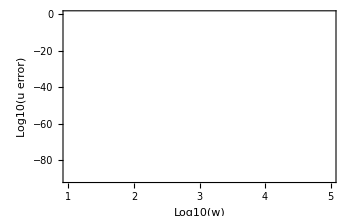

```mathematica
K=MasterStiffnessOfSixElementBar[100];f={1,2,3,4,5,6,7};
Print["Master Stiffness K=",K//MatrixForm];Print["Applied forces=",f];uexact={0,0.27,0.275,0.25,0.185,0.07,0.14};ew={};For [w=100,w≤10^16,w=10*w;Khat=K;fhat=f;Khat[[2,2]]+=w;Khat[[6,6]]+=w;Khat[[6,2]]=Khat[[2,6]]-=w;fhat[[2]]+=(1/5)*w;fhat[[6]]-=(1/5)*w;{Kmod,fmod}=FixLeftEndOfSixElementBar[Khat,fhat];u=uhat=LinearSolve[N[Kmod],N[fmod]];Print["Weight w=",N[w]//ScientificForm];e=Sqrt[(u-uexact).(u-uexact)];Print["L2 solution error=",e//ScientificForm];AppendTo[ew,{Log[10,w]Log[10,e]}];
];
ListPlot[ew,AxesOrigin->{5,-8},Frame->True,PlotStyle->{AbsolutePointSize[4],AbsoluteThickness[2],RGBColor[1,0,0]},Joined->True,ImageSize->350,AxesLabel->{"Log10(w)","Log10(u error)"}]
```